# Floquet optical lattice

## Introduction to Floquet

For a fantastic reference/tutorial on Floquet theory of optical lattices and how to calculate quasienergy spectra, see “Floquet engineering with quasienergy bands of periodically driven optical lattices” by Martin Holthaus (link here). The paper also has a cool review of how Bloch energy bands have an analytic solution through the Mathieu equations, something Holger has pointed out in the past. Everything below is based off of the numerical procedure outlined in this paper. 

Floquet theory is useful for studying any problem with a time-periodic Hamiltonian

H(t) = H(t+T).

There is a deep relationship between Floquet theory and the standard theory of spatial crystals. For Floquet systems, we essentially have a time crystal (different from the sense of time crystal as used in Norm's paper...), in analogue to a spatial crystal for which we would have

H(x) = H(x + λ), 

where λ is the periodicity of the spatial crystal. Periodicity in space naturally gives rise to the idea of quasimomentum, which is a quantum number that is constrained to the first Brillioun Zone {-ℏk/2, ℏk/2} (where here k is defined as k = 2π/λ). In such a crystal, momentum can only be transferred as integer multiples of k. Analogously, a Floquet Hamiltonian driven at frequency ω can be described by quasienergy, which is restricted to the first energy Brillion zone (for lack of a better word) bounded by {-ℏω/2, ℏω/2}. In the Floquet case, energy can only be transferred in integer multiples of ℏω. 

Both quasimomentum and quasienergy require us to fold energy bands back into the first Brillioun zone: for spatial lattices we fold along the momentum axis, for floquet lattices we fold along the energy axis. Folding bands into the same Brillion zone necessarily results in band crossings, and the coupling between levels that the floquet drive provides will open these up into avoided level crossings. The energy gap formed at the level crossing is depends on the coupling. In both cases, higher-order (muli-photon) processes result in weaker coupling, resulting in much smaller energy gaps at the band crossings.

For a full treatment of Floquet calculations and derivations, see the above reference. Here, I just describe the main results and how to calculate a quasienergy spectrum.

## Calculate quasienergy spectrum

The time evolution operator 

U(t+T,t)

ends up being of central importance to the analysis. It is important because, if you start with any state vector ψ(t) this operator tells you the state at time t+T:

ψ(t+T) = U(t+T, t) ψ(t)

Since our Hamiltonian is periodic in time, we can just keep repeatedly applying this time evolution operator each time step and it will tell us the new state and the end of each period. But, this matrix itself is independent of time since we have, in effect, integrated over the time variation! Since the matrix is independent of time, we can look for eigenstates of the matrix, ie. states which end up mapped back to themselves after an evolution of time T = 2π/ω. These are the eigenstates of the Floquet system, and will remain eigenstates after any integer number of periods T. The eigenvalues of this matrix are of the form 

e^(-ⅈ ϵ_n T/ℏ)

where ϵ_n is the quasienergy of the Floquet eigenstates. Note that all of these eigenvalues will have unit length because U must be a unitary operator, and one must take the phase argument of the eigenvalues to get the actual quasienergy.

So, how do we solve for this spectrum in practice? It ends up being easiest to solve for the time evolution of some set of basis states for the period of the drive T = (2π)/ω. The solved vectors are stacked together into a time evolution unitary matrix U(T). This has a simple interpretation: we are just construction a matrix that describes the mapping between the initial basis states to some new states after time T. The matrix U(T) can then be diagonalized to solve for the quasienergies.

Below, I set up a couple modules to

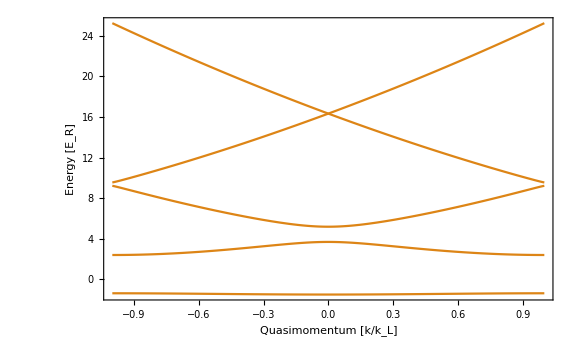

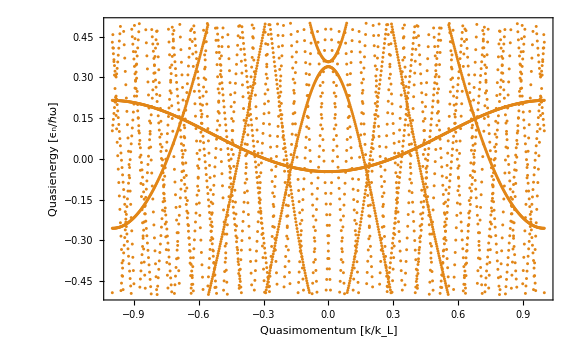

```mathematica
Clear[kMax,dim]

SortU[UMat_,dimen_] := Module[{U = UMat, dim = dimen},
USquared = Transpose[Abs[U⟦#⟧]^2 &/@Range[dim]];
swap[i_,j_]:=(U=ReplacePart[U,{i->U⟦j⟧,j->U⟦i⟧}]);

For[m=1,m<dim, m++,
indexMax = Ordering[USquared⟦m⟧, -1]⟦1⟧;
swap[m,indexMax];
];
U
]

PlotFloquetSweep[sweepList_, Hammy_, evaluate_,plotTitle_] := Module[{sweep = sweepList, Ham = Hammy, eval = evaluate, T = (2π)/ω/.evaluate, dim = 2kMax+1/.evaluate,kMax = kMax/.evaluate, title = plotTitle},

quasiEVals = Table[0, Length[sweep],dim];

For[i=1, i≤Length[sweep], i++,

U = Table[0,dim,dim];

For[j = 1, j≤ dim,j++,
ψi = Table[0,dim];
ψi⟦j⟧ = 1;

Clear[ci, ψ,cs];
ψ[t_]=Table[ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];

(* Solve the main Schrodinger equation for one period of the floquet drive *)
(*InitBandsSorted⟦2⟧⟦j⟧*)
ics = Table[ci[n][0]==ψi⟦n + (kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ (Ham[sweep⟦i⟧, t]/.eval).ψ[t];
soln = NDSolve[{equation,ics},cs,{t,0,T}];
ψf[t_]=ψ[t]/.soln⟦1⟧;

U⟦j⟧ = ψf[T];
];

(*U = SortU[U,dim];*)

FloquetBands = Eigensystem[Transpose@U];
quasiEVals⟦i⟧ = -Arg[FloquetBands⟦1⟧]/(2π);
];

ListPlot[Transpose[{sweep,Transpose[quasiEVals]⟦#⟧}]&/@Table[i,{i,1,dim}], ImageSize->Large, Frame->True, FrameLabel->{title,"Quasienergy [ϵ_n/ℏω]"}, PlotStyle->ColorData[98,"ColorList"]⟦2⟧]
];

evalKs = {kMax -> 2,α-> 0.2,V0->8,ω-> 0.5, β-> 0.76};
kList = Range[-1, 1, 0.0025];

Ham[α_, k0_, t_,kMax_] := Hold@Normal[SparseArray[{{m_,m_}:>(k0 + 2(m - (kMax+1)))^2 ,{i_,j_}:>V0/4(1+α Sin[ω t])/;Abs[i-j]==1},{2 kMax+1,2 kMax+1}]];
HamKs[k0_,t_] = ReleaseHold[Ham[α,k0,t,kMax]/.evalKs];

p1 = Plot[Eigenvalues[ReleaseHold[Ham[α,k,0,kMax]/.evalKs]], {k, -1,1}, Frame->True, FrameLabel->{"Quasimomentum [k/k_L]", "Energy [E_R]"}, ImageSize->Large]
p2 = PlotFloquetSweep[kList, HamKs, evalKs,"Quasimomentum [k/k_L]"]
```

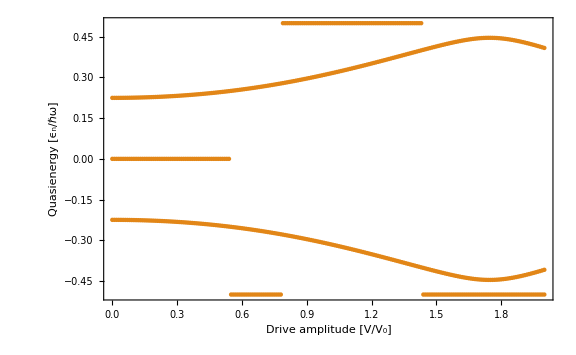

```mathematica
evalαs = {kMax -> 1,V0->4,ω-> 2, T-> (2π)/2,k0->0};
αList = Range[0, 2, 0.01];
Hamαs[α_,t_] = ReleaseHold[Ham[α,k0,t,kMax]/.evalαs];
PlotFloquetSweep[αList, Hamαs, evalαs, "Drive amplitude [V/V_0]"]
```

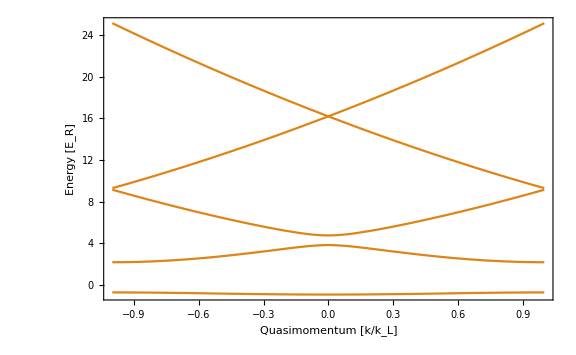

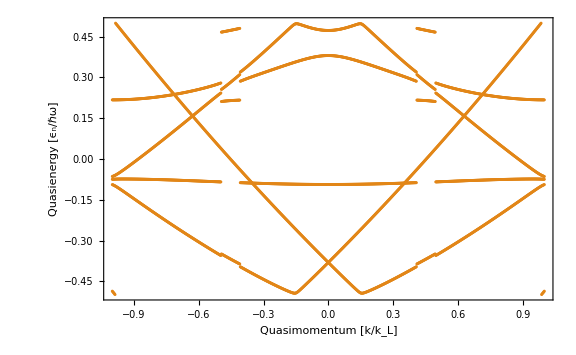

```mathematica
HamShake[α_, k0_, t_,kMax_] := Hold@Normal[SparseArray[{{m_,m_}:>(k0 + β Sin[ω t] + 2(m - (kMax+1)))^2 ,{i_,j_}:>V0/4/;Abs[i-j]==1},{2 kMax+1,2 kMax+1}]];
HamKs[k0_,t_] = ReleaseHold[Ham[α,k0,t,kMax]/.evalKs];

p1 = Plot[Eigenvalues[ReleaseHold[Ham[α,k,0,kMax]/.evalKs]], {k, -1,1}, Frame->True, FrameLabel->{"Quasimomentum [k/k_L]", "Energy [E_R]"}, ImageSize->Large]
p2 = PlotFloquetSweep[kList, HamKs, evalKs,"Quasimomentum [k/k_L]"]
```

## Try operator approach to computing quasienergy spectrum

This is based off the technique used in the Matlab code given to me by the Weld group at UCSB

```mathematica
(*General strategy for sorting is to compute unperturbed eigenvectors, then project onto those states. *)
SortU[UMat_,Hammy_,evaluate_] := Module[{U = UMat, Ham = Hammy, dim = 2 kMax+1/.evaluate, ω = ω/.evaluate},
	(*Find eigenstystem for the unperturbed Hamiltonian, then sort*)
	OGeigs = Eigensystem[Ham];
	OGeigs = Transpose@SortBy[Transpose@OGeigs,First];

	(*Eigensystem of the time evolution matrix. We want to sort these eigenvalues*)
	Ueigs = Eigensystem[U];

	(*Calculate overlap of columns of U with the eigenvectors*)
	overlap = Abs[Transpose[Ueigs⟦2⟧].OGeigs⟦2⟧]^2;
	
	(*Now swap columns of Ueigs in order of overlaps*)
	order = Transpose[Ordering[overlap⟦#⟧,-1]&/@Range[dim]]⟦1⟧; (*This calculates the order in which the OG eigenvalues overlap with Ueigs*)
	Ueigs = Transpose[Transpose[Ueigs]⟦#⟧&/@order];

	Ueigs
];

PlotFloquetKsSweep[sweepList_, Hammy_, evaluate_,plotFloquet_:True] := Module[{sweep = sweepList, Ham = Hammy, eval = evaluate, T = (2π)/ω/.evaluate, dim = 2kMax+1/.evaluate,kMax = kMax/.evaluate, ω = ω/.evaluate},

	(*Initialize storage of calclated eigenvalues *)
quasiEVals = Table[0, Length[sweep],dim];

	(*Loop over swept list*)
For[i=1, i≤Length[sweep], i++,

	(*Initialize time evolution matrix and exponentiated Hamiltonian matrices *)
	UT = IdentityMatrix[2 kMax + 1, SparseArray]/.eval;
	HamExp = MatrixExp[-ⅈ Ham[sweep⟦i⟧, 0]]; (*This is to pre-allocate memory *)
	tStep = T/nSteps;

	(*Loop over number of time steps nSteps in the time evolution matrix calculation *)
	For[j=1,j≤ nSteps,j++, 
			tCurrent = (j-1/2)tStep;
			HamExp = MatrixExp[-ⅈ Ham[sweep⟦i⟧, tCurrent]tStep];
			UT = HamExp.UT;
	];
(*   Doesn't work   *)(*
SortedBands = SortU[UT,Ham[sweep⟦i⟧,0],eval];*)

	(*calculate quasienergy values and return *)
quasiEVals⟦i⟧ = -Arg[Eigenvalues[UT]]/(2π);
];
	(*Sorted eigenvalues of unperturbed Hamiltonian*)
	SortedEigs[k_]:=Transpose[SortBy[Transpose[Eigensystem[Ham[k,0]]], First]]⟦1⟧;
	SortedQuasiEigs[k_]:=(Mod[SortedEigs[k]+ω/2,ω] - ω/2)/ω;

	(*Make plot of floqeut eigenvalues from sweeping k *)
	sweepPlot = ListPlot[Transpose[{sweep,Transpose[quasiEVals]⟦#⟧}]&/@Table[i,{i,1,dim}], ImageSize->Large, Frame->True, FrameLabel->{"Quasimomentum [k/k_L]","Quasienergy [ϵ_n/ℏω]"}, PlotStyle->ColorData[98,"ColorList"]⟦1⟧, PlotLegends->{"Floquet Bands"}];
	
	(*Make plot of original eigenvalues folded into quasienergy zone *)
	OGPlot[eigs_, color_] := Plot[Evaluate@eigs[k], {k, -1,1}, Frame->True, FrameLabel->{"Quasimomentum [k/k_L]", "Energy [E_R]"}, ImageSize->Large, PlotStyle->color, PlotLegends -> {"Original bands"}, PlotRange->All,Exclusions->Flatten[{(eigs[k]⟦#⟧ - eigs[k+0.02]⟦#⟧)/0.1==0.5, (eigs[k]⟦#⟧ - eigs[k+0.02]⟦#⟧)/0.1==-0.5}&/@Range[1,dim]]];

	(* Make plot of OG eigs *)
	OGEigsPlot = OGPlot[SortedEigs, ColorData[98,"ColorList"]⟦2⟧];

	(*Show final plots*)
	Show[OGEigsPlot]
	
	If[plotFloquet,
		Show[{Evaluate@OGPlot[SortedQuasiEigs, RGBColor[0.39,0.39,0.39]], sweepPlot}],##&[]
	]
];

PlotFloquetSweep[sweepList_, Hammy_, evaluate_,plotTitle_] := Module[{sweep = sweepList, Ham = Hammy, eval = evaluate, T = (2π)/ω/.evaluate, dim = 2kMax+1/.evaluate,kMax = kMax/.evaluate, title = plotTitle, ω = ω/.evaluate},

	(*Initialize storage of calclated eigenvalues *)
quasiEVals = Table[0, Length[sweep],dim];

	(*Loop over swept list*)
For[i=1, i≤Length[sweep], i++,

	(*Initialize time evolution matrix and exponentiated Hamiltonian matrices *)
	UT = IdentityMatrix[2 kMax + 1, SparseArray]/.eval;
	HamExp = MatrixExp[-ⅈ Ham[sweep⟦i⟧, 0]]; (*This is to pre-allocate memory *)
	tStep = T/nSteps;

	(*Loop over number of time steps nSteps in the time evolution matrix calculation *)
	For[j=1,j≤ nSteps,j++, 
			tCurrent = (j-1/2)tStep;
			HamExp = MatrixExp[-ⅈ Ham[sweep⟦i⟧, tCurrent]tStep];
			UT = HamExp.UT;
	];
(*   Doesn't work   *)(*
SortedBands = SortU[UT,Ham[sweep⟦i⟧,0],eval];*)

	(*calculate quasienergy values and return *)
quasiEVals⟦i⟧ = -Arg[Eigenvalues[UT]]/(2π);
];
	(*Make plot of floqeut eigenvalues from sweeping the sweep parameter *)
	sweepPlot = ListPlot[Transpose[{sweep,Transpose[quasiEVals]⟦#⟧}]&/@Table[i,{i,1,dim}], ImageSize->Large, Frame->True, FrameLabel->{title,"Quasienergy [ϵ_n/ℏω]"}, PlotStyle->ColorData[98,"ColorList"]⟦3⟧]

];
```

### AM optical lattice

Let’s use this on an AM optical lattice, with Hamiltonian

 Ĥ = p^2/(2 M) + V_0/4[1+α sin(ω t)]cos(2 x) 

where  α  is a dimensionless driver parameter,  ω  is the drive frequency, and  V_0  is the lattice depth.

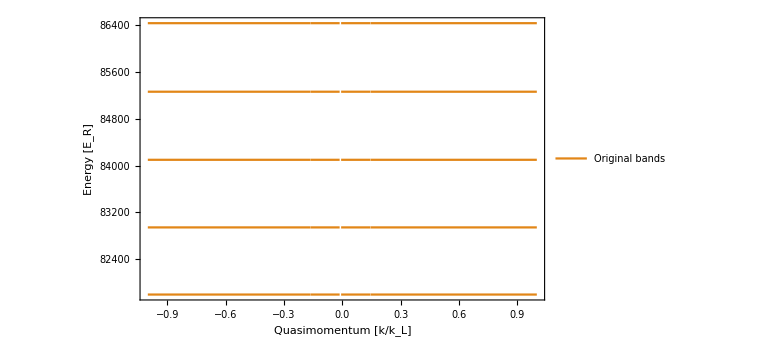
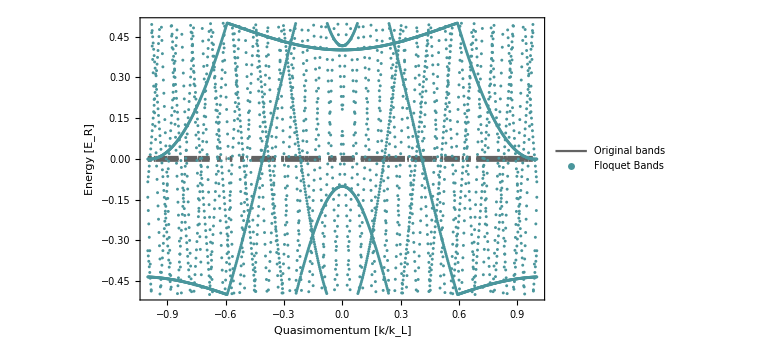

```mathematica
nSteps = 30; (*This is the number of time steps to use in the range t = {0, (2π)/ω} when computing the time evolution operator*)

evalAM = {kMax -> 2,α->0.6,V0->8,ω-> 0.5};
kList = Range[-1, 1, 0.0025];

HamAM[α_, k0_, t_,kMax_] := Hold@Normal[SparseArray[{{m_,m_}:>(k0 + 2(m - (kMax+1)))^2 ,{i_,j_}:>V0/4(1+α Sin[ω/2 t]^2)/;Abs[i-j]==1},{2 kMax+1,2 kMax+1}]];
HamAMKs[k0_,t_] = ReleaseHold[HamAM[α,k0,t,kMax]/.evalAM];

p2 = PlotFloquetKsSweep[kList, HamAMKs, evalAM]
```

### Shaken Lattice

This plots what happens in k-space when you shake the lattice, instead of amplitude modulate it. You can think of amplitude modulating as trying to shake in both directions at the same time. The Hamiltonian for shaking is 

  H_shake = (p + β sin(ω t))^2/(2 M) +V_0/4 cos(2 k x)  



  H_sha   

where β is the drive parameter and  V_0  the lattice depth.

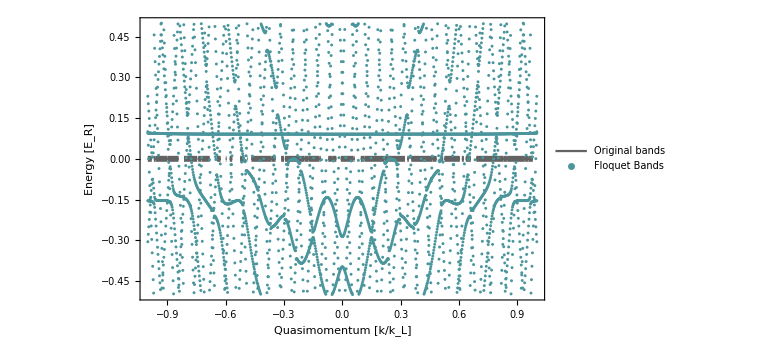
-Graphics- -Graphics-

```mathematica
evalShaken = {kMax ->2 ,V0->8,ω->0.5,β->0.77};

HamShaken[β_, k0_, t_,kMax_] := Hold@Normal[SparseArray[{{m_,m_}:>(k0 + β Sin[ω t] +  2(m - (kMax+1)))^2 ,{i_,j_}:>V0/4/;Abs[i-j]==1},{2 kMax+1,2 kMax+1}]];
HamShakenKs[k0_,t_] = ReleaseHold[HamShaken[β,k0,t,kMax]/.evalShaken];

p2 = PlotFloquetKsSweep[kList, HamShakenKs, evalShaken]
```

## Two commensurate lattices

### Shake the first harmonic

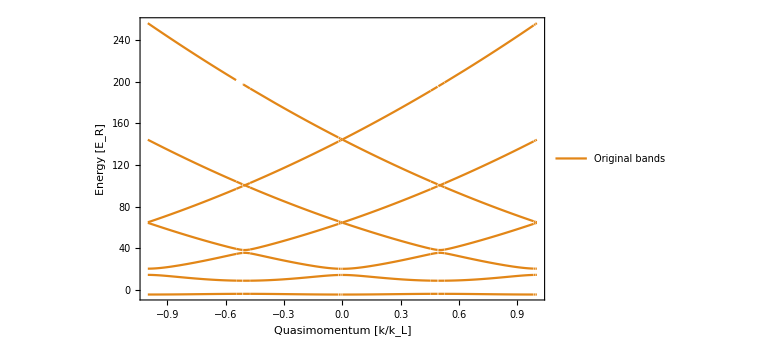

```mathematica
(* Note that the Hamiltonian dimension is dim = 2*kMax + 1 to keep the dimensionality the same as before (so I can resuse functions from about). But since we now have k and 2k wavenumbers, I scale momentum by 1/2 so that we can fit inside the BZ with quasimomentum of {-1,1}  *)
evalFHShaken = {kMax -> 3,V0->20,V1->20,ω->10,β->0.3, ϕFH ->π/2};

HamFHShaken[β_, k0_, t_,kMax_] := Hold@Normal[SparseArray[{{m_,m_}:>4(2 k0 +2(m - (kMax+1)))^2 ,{i_,j_}:>V1/4/;Abs[i-j]==2,{a_,b_}:>V0/4 Exp[ⅈ (ϕFH +β Sin[ω t])]/;a-b==1,{c_,d_}:>V0/4 Exp[-ⅈ (ϕFH +β Sin[ω t])]/;d-c==1},{2 kMax+1,2 kMax+1}]];
HamFHShakenKs[k0_,t_] = ReleaseHold[HamFHShaken[β,k0,t,kMax]/.evalFHShaken];

PlotFloquetKsSweep[kList, HamFHShakenKs, evalFHShaken, False]
```

### AM the first harmonic

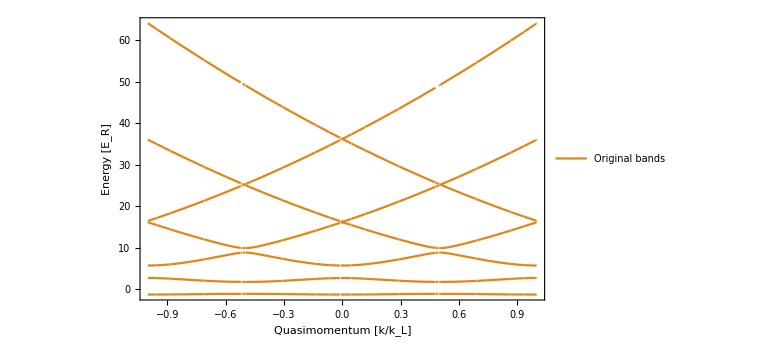
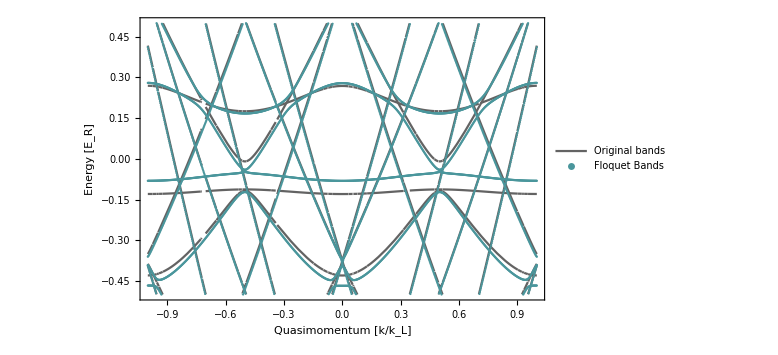

```mathematica
(* Note that the Hamiltonian dimension is dim = 2*kMax + 1 to keep the dimensionality the same as before (so I can resuse functions from about). But since we now have k and 2k wavenumbers, I scale momentum by 1/2 so that we can fit inside the BZ with quasimomentum of {-1,1}  *)
evalFHAM = {kMax ->3,V0->4,V1->4,ω->10,β->1, ϕFH ->0};

HamFHAM[β_, k0_, t_,kMax_] := Hold@Normal[SparseArray[{{m_,m_}:>4(k0 +(m - (kMax+1)))^2 ,{i_,j_}:>V1/4/;Abs[i-j]==2,{a_,b_}:>V0/4 Exp[ⅈ ϕFH](1+β Cos[ω/2 t]^2)/;a-b==1,{c_,d_}:>V0/4 Exp[-ⅈ ϕFH](1+β Cos[ω/2 t]^2)/;d-c==1},{2 kMax+1,2 kMax+1}]];
HamFHAMKs[k0_,t_] = ReleaseHold[HamFHAM[β,k0,t,kMax]/.evalFHAM];

PlotFloquetKsSweep[kList, HamFHAMKs, evalFHAM]
```